Catenate::invrp: The argument MWTMStep[{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{1,0}→{1,1,1}},{{1,3},{0,0,0,0,0}}] is not a valid Association or a list.

Union::heads: Heads Catenate and List at positions 2 and 1 are expected to be the same.

{{{{1,3},{0,0,0,0,0}}},{{{1,3},{0,0,0,0,0}}}∪Catenate[{MWTMStep[{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{1,0}→{1,1,1}},{{1,3},{0,0,0,0,0}}]}],{{{1,3},{0,0,0,0,0}}}∪Catenate[{MWTMStep[{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{1,0}→{1,1,1}},{{1,3},{0,0,0,0,0}}]}]∪Catenate[MWTMStep[Catenate[{MWTMStep[{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{1,0}→{1,1,1}},{{1,3},{0,0,0,0,0}}]}],{{{1,3},{0,0,0,0,0}}},{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{1,0}→{1,1,1}}]]}

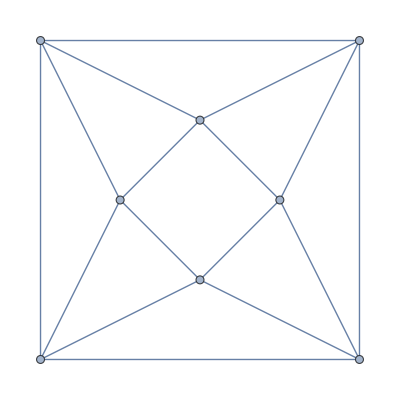

```mathematica
/* pseudocode 

record handpan wave files (done) 
split handpan wave files into distinct files
load d minor handpan wave files as playable in mathematica
map hand wave files to multiway states
create simple multiway evolution
create secondary state graph  to match 'commonly played sequences' or 'sequences perceived as beautiful' (c.f. Wolfram games article, sequences could mirrors this, winning conditions could be 'perceived as beautiful' )
convert to rulial space
allow for variability in wave form (i.e. translator from sound to waveform) 

*/




MWTMEvolveList[{{1, 1} -> {1, 0, -1}, {1, 0} -> {1, 0, -1}, {1, 
    0} -> {1, 1, 1}}, {{{1, 3}, {0, 0, 0, 0, 0}}}, 2]


GraphData[{"Antiprism", 4}]
```

```mathematica
ResourceFunction[
 "MultiwayTuringMachine"][{2506, 3506}, {{1, 1, 0}, {0, 1, 0, 0}}, 3, "StatesGraph", VertexSize -> 1]


h = PathGraph[First[FindHamiltonianCycle[g]]];
Row[{HighlightGraph[g, h, GraphHighlightStyle -> "Thick"], 
  Graphics3D[{Opacity[.8], 
    PolyhedronData["Dodecahedron", "GraphicsComplex"], Red, 
    Tube[PolyhedronData["Dodecahedron", "Vertices", "Coordinates"][[
      Append[VertexList[h], VertexList[h][[1]]]]], 0.1]}]}, 
 Spacer[10]]
```

-Graphics-

VertexList::graph: A graph object is expected at position 1 in VertexList[PathGraph[g]].

VertexList::graph: A graph object is expected at position 1 in VertexList[PathGraph[g],PathGraph[g]].

General::stop: Further output of VertexList::graph will be suppressed during this calculation.

Part::pkspec1: The expression VertexList[PathGraph[g],PathGraph[g]] cannot be used as a part specification.

HighlightGraph[g,PathGraph[g],GraphHighlightStyle→Thick]-Graphics3D-

```mathematica
CloudGet["https://www.wolframcloud.com/obj/sw-blog/MultiwayTuringMachines/Programs-01.wl"];
MWTMEvolveList[rule_, inits : {{{_, _}, _} ...}, t_Integer] :=
 NestList[Union[#, Catenate[Map[MWTMStep[rule, #] &, #]]] &, inits, t]
 
 
 MWTMEvolveList[rule_, inits : {{{_, _}, _} ...}, t_Integer] :=
 NestList[Union[#, Catenate[Map[MWTMStep[rule, #] &, #]]] &, inits, t]
```